```mathematica
SetDirectory["~/Documents/GitHub/AvoidedQP/1chain/"]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/1chain

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
s=4/3;
sf=1.17;
```

```mathematica
getAssoc[filename_]:=(
result={};
Do[(
file=StringJoin[filename,".json"];
sData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,sData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
interchainAvail=Normal[DeleteDuplicates[ds[Take,"magnonmagnon"]]];
<|"size"->sizeAvail,"coupling" ->couplingAvail,"magnonmagnon"->interchainAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_]:=(
data=Apply[ds,directive];
{x,y}=Table[(data[Take,keys[[i]]]//Normal)[[1]],{i,1,2}];

Return[Table[{x[[i]],y[[i]]/y[[sizeAvail[[1]]]]},{i,sizeAvail[[1]],Length[x]}]]
)
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,IntegerPart[x],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
getDPlot[spc_,n_]:=(
SetOptions[MaTeX,Magnification->1.6 s sf];

fs=22;
tckn=0.005;
legends=ToString/@StandardNumberForm/@(Round[1/Normal[spcAvail["magnonmagnon"]]-1,0.01]);
latexlegends=MaTeX/@Table["J_\\perp / J_\\parallel = "<>entry,{entry,legends}];

SetOptions[MaTeX,Magnification->0.8*1.5s sf];

plt=ListPlot[spc,
SetOptions[LinTicks,TickLengthScale->1.5];
ImageSize->360,
Joined->False,
PlotMarkers->If[λ==spcAvail["magnonmagnon"][[1]],
{"◆",12s*0.75},
If[λ==spcAvail["magnonmagnon"][[3]],
{"▼",12s*0.75},
{"▲",12s*0.75}
]],
PlotStyle->
If[λ==spcAvail["magnonmagnon"][[1]],
Lighter[Blend[{Orange,Red},0.75]],
If[λ==spcAvail["magnonmagnon"][[3]],
Lighter[Blend[{Red,Purple},0.75]],
Lighter[Blend[{Red,Purple},0.25]]
]
],
Frame->True,Axes->False,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
LabelStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
PlotRange->{{0,n-1},{10^-(17),9.9}},
PlotRangeClipping->False,
FrameLabel->MaTeX@{"n","-\\log_{10}(c_n / c_0)"},
PlotLegends->Placed[PointLegend[Automatic,latexlegends,Spacings->0],Scaled[{0.8, 0.45}]],
ClippingStyle->Automatic,
AspectRatio->0.85,
Epilog->{
Inset[
MaTeX["\\text{(a)}"],
Scaled[{0.2,0.65}]],
Inset[
MaTeX["\\text{(b)}"],
Scaled[{0.65,0.2}]]
},
ScalingFunctions->"Log",
FrameTicks->{{Table[{10^-l,If[Mod[l,2]==0,MaTeX[l],""]},{l,-10,20,1}],Table[{10^-l,""},{l,-10,20,1}]},{LinTicks[-30,30,10,10,TickLabelFunction->tlf],LinTicks[-30,30,10,10,ShowTickLabels->False]}}
];

plt
)
```

```mathematica
makePlotsSpc[]:=(
dirc={Select[#magnonmagnon==λ&]};
keys={"magnons","coefficients"};

plots={};
Do[(
spc=extractData[spcDataset,dirc,keys];
AppendTo[plots,getDPlot[{spc},Normal[spcAvail["size"]][[1]]]];
),{λ,spcAvail["magnonmagnon"]//Normal}];


plots
)
```

```mathematica
filelist={
"cn_28_3"
};
spcPlots={};
Do[(
spcDataset=Dataset[getAssoc[filename]];
spcAvail=Dataset[getStruct[spcDataset]];
AppendTo[spcPlots,makePlotsSpc[]];
),{filename,filelist}]
```

```mathematica
spcAvail
```

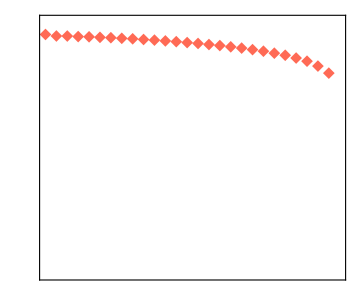
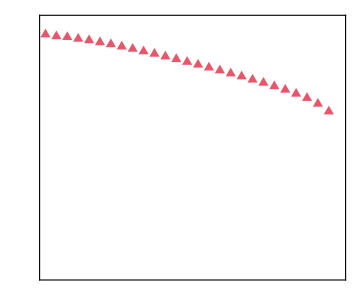
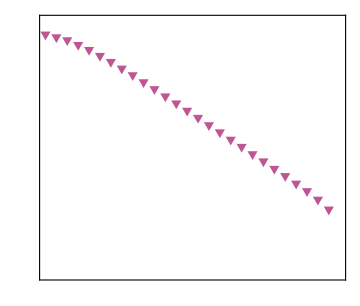

```mathematica
spcPlots
```

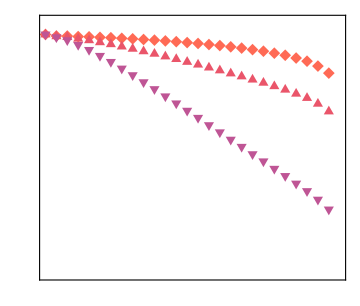

```mathematica
fs=22;
SetOptions[MaTeX,Magnification->1.25s sf];
pltjoint=Legended[Show[spcPlots[[1]]],
Placed[PointLegend[Reverse[{Lighter[Blend[{Orange,Red},0.75]],Lighter[Blend[{Red,Purple},0.25]],Lighter[Blend[{Red,Purple},0.75]]}],
MaTeX@Reverse[{"J_\\perp = 0.01J","J_\\perp = 0.1J","J_\\perp = 0.5J"}],
LegendMarkerSize->16,Spacings->0.0,
LegendMarkers->Reverse[{{"◆",12s*0.75},{"▲",12s*0.75},{"▼",12s*0.75}}]],
{0.27,0.22}]
]
```

```mathematica
(*Export["./plots/"<>"cn_28_3"<>".png",pltjoint,ImageResolution->300]*)
```